Motion of projectile near the surface of earth with air resistance F_v= -k v

Use Mathematica to solve the equations of motion analytically:

```mathematica
sol = DSolve[
{
vx'[t]== -k vx[t],                (*  acceleration *)
vy'[t]== -k vy[t]-g,
x'[t]== vx[t],                         (* velocities    *)
y'[t]== vy[t],
vx[0]== v0x,vy[0]== v0y,x[0]== 0,y[0]== 0 (* Initial Conditions *)
},{vx,vy,x,y},t]
```

{{vx→Function[{t},ⅇ^(-k t) v0x],x→Function[{t},(ⅇ^(-k t) (-1+ⅇ^(k t)) v0x)/k],vy→Function[{t},-(ⅇ^(-k t) (-g+ⅇ^(k t) g-k v0y))/k],y→Function[{t},-(ⅇ^(-k t) (g-ⅇ^(k t) g+ⅇ^(k t) g k t+k v0y-ⅇ^(k t) k v0y))/k^2]}}

Define the functions of velocity and position:

```mathematica
vx[t_] = vx[t] /.sol[[1,1]];
vy[t_] = vy[t] /.sol[[1,3]];
x[t_] = x[t]/.sol[[1,2]];
x[t_] = x[t]/.sol[[1,2]];
```

ⅇ^(-k t) v0x

```mathematica
Print["v_x(t)= ",vx[t]                    ,   "        v_y(t)= ",vy[t]//Expand,
         "\nx(t)= ",x[t]//Expand,   "         y(t)= ",y[t]//Expand]
```

v_x(t)= ⅇ^(-k t) v0x        v_y(t)= -g/k+(ⅇ^(-k t) g)/k+ⅇ^(-k t) v0y
x(t)= v0x/k-(ⅇ^(-k t) v0x)/k         y(t)= g/k^2-(ⅇ^(-k t) g)/k^2-(g t)/k+v0y/k-(ⅇ^(-k t) v0y)/k

Define the numerical values of the parameters that you want to use in the plots here:

```mathematica
parameters = {v0x ->  √2,v0y -> √2,k-> 5, g-> 9.81}
```

{v0x→√2,v0y→√2,k→5,g→9.81}

Plot of velocities. We show the asymptotic value of v_(0y).

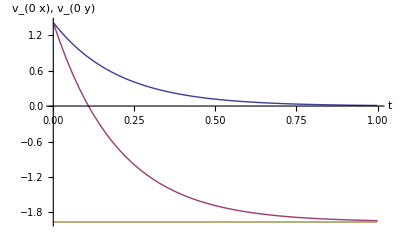

```mathematica
Plot[Evaluate[{vx[t],vy[t],-g/k}/.parameters],{t,0 ,1},AxesLabel-> {"t","v_(0  x), v_(0  y)"}]
```

Plot the positions. We show the asymptotes x=(v_(0x))/k and y=-g/kt+(g/k^2+(v_(0y))/k)

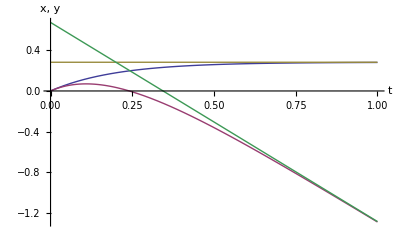

```mathematica
Plot[Evaluate[{x[t],y[t],v0x/k,-g/k t + g/k^2+v0y/k}/.parameters],{t,0 ,1},AxesLabel-> {"t","x, y"}]
```

The trajectory: We see that x=(v_(0x))/k is a vertical asymptote. On this the particle moves with almost constant verlocity, the limit velocity v_lim.

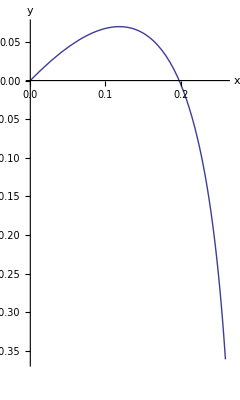

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.parameters],{t,0,0.5},AxesLabel-> {"x","y"}]
```